```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY190/sec_int_data/500nm.dat"]
```

{{1.16196,0.32288},{1.1485,0.320343},{1.13288,0.312399},{1.11879,0.289605},{1.10986,0.257352},{1.10188,0.225301},{1.0953,0.2205},{1.09118,0.218734},{1.08898,0.242475},{1.08844,0.266126},{1.08969,0.295353},{1.094,0.315467},{1.09832,0.315978},{1.10319,0.32952},{1.11502,0.318672},{1.13408,0.336115},{1.14571,0.32317},{1.16039,0.332106},{1.17699,0.329735},{1.19764,0.320415},{1.21871,0.317581},{1.24216,0.319035},{1.26543,0.320488},{1.29691,0.315176},{1.32536,0.293341},{1.37118,0.288482},{1.45421,0.260208}}

0.238317+0.0497049 x

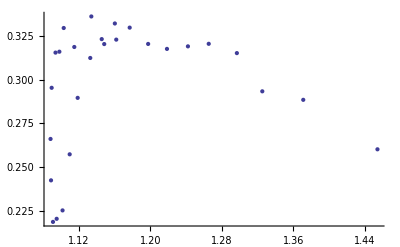

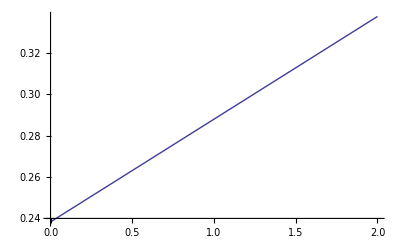

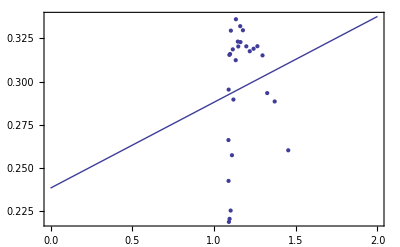

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```